## cool

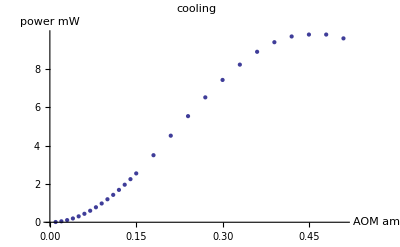

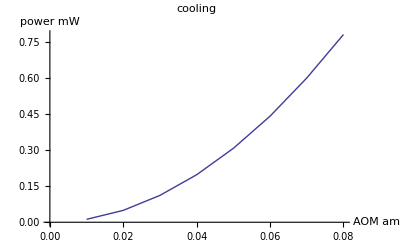

```mathematica
bkgrd=0.039/1000;
cool={{0.01,12.13/1000},
{0.02,49.5/1000},
{0.03,112/1000},
{0.04,198/1000},
{0.05,308/1000},
{0.06,442/1000},
{0.07,601/1000},
{0.08,782/1000},
{0.09,0.98},
{0.1,1.20},
{0.11,1.43},
{0.12,1.69},
{0.13,1.96},
{0.14,2.25},
{0.15,2.55},
{0.18,3.50},
{0.21,4.52},
{0.24,5.54},
{0.27,6.52},
{0.3,7.43},
{0.33,8.23},
{0.36,8.9},
{0.39,9.4},
{0.42,9.7},
{0.45,9.8},
{0.48,9.8},
{0.51,9.6}};
cool2=cool[[;;,2]]-bkgrd;
cool3=Thread[{cool[[;;,1]],cool2}];
ListPlot[cool3,AxesLabel->{"AOM amp","power mW"},PlotLabel->"cooling"]
ListPlot[cool3[[;;8]],Joined->True,AxesLabel->{"AOM amp","power mW"},PlotLabel->"cooling"]
```

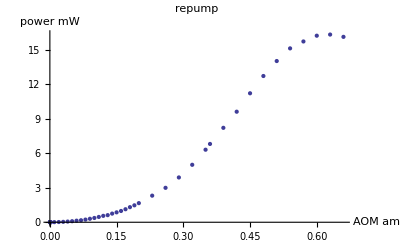

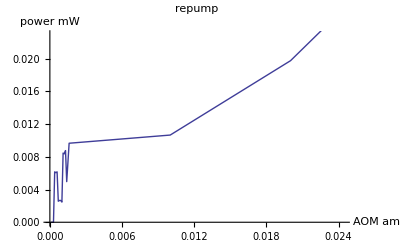

```mathematica
bkgrd=0.031/1000;
rp={{0.0001,0.031/1000},
{0.0002,0.031/1000},
{0.0003,0.031/1000},
{0.0004,6.2/1000},
{0.0005,6.1/1000},
{0.0006,6.2/1000},
{0.0007,2.6/1000},
{0.0008,2.7/1000},
{0.0009,2.7/1000},
{0.001,2.5/1000},
{0.0011,8.5/1000},
{0.0012,8.4/1000},
{0.0013,8.8/1000},
{0.0014,5/1000},
{0.0014,5/1000},
{0.0016,9.7/1000},
{0.01,10.7 /1000},
{0.02,19.8/1000},
{0.03,34.2/1000},
{0.04,60.1/1000},
{0.05,91/1000},
{0.06,136/1000},
{0.07,173/1000},
{0.08,231/1000},
{0.09,303/1000},
{0.1,372/1000},
{0.11,461/1000},
{0.12,556/1000},
{0.13,617/1000},
{0.14,751/1000},
{0.15,0.86},
{0.16,0.98},
{0.17,1.13},
{0.18,1.31},
{0.19,1.47},
{0.2,1.66},
{0.23,2.31},
{0.26,2.99},
{0.29,3.89},
{0.32,4.99},
{0.35,6.3},
{0.36,6.8},
{0.39,8.2},
{0.42,9.6},
{0.45,11.2},
{0.48,12.7},
{0.51,14.0},
{0.54,15.1},
{0.57,15.7},
{0.6,16.2},
{0.63,16.3},
{0.66,16.1}};
rp2=rp[[;;,2]]-bkgrd;
rp3=Thread[{rp[[;;,1]],rp2}];
ListPlot[rp3,AxesLabel->{"AOM amp","power mW"},PlotLabel->"repump"]
ListPlot[rp3[[;;20]],Joined->True,AxesLabel->{"AOM amp","power mW"},PlotLabel->"repump"]
```